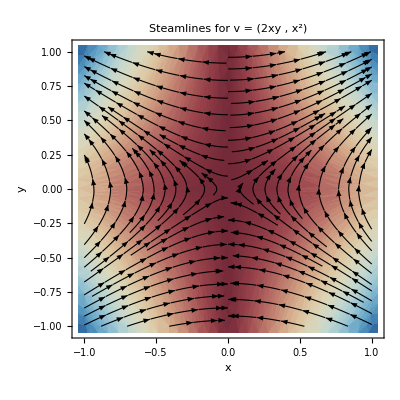

∇·v⃗ = 2 y

The flow is Compressible

∇× v⃗ = {0,0,0}

The flow has No Vorticity

```mathematica
Remove["Global`*"]
v={2 x y,x^2};
StreamDensityPlot[v,{x,-1,1},{y,-1,1},ColorFunction->"RedBlueTones",StreamStyle->{Black,Thickness[.002]},PlotLabel->Style["Steamlines for v = (2xy , x^2)",15,"Graphics"],FrameLabel->{"x","y"} ]
Print["∇·v⃗ = ",Div[Flatten[{v,0}],{x,y,z}]]
Print["The flow is ",Evaluate[If[TrueQ[Div[Flatten[{v,0}],{x,y,z}]==0],Style["Incompressible",Bold],Style["Compressible",Bold]]]]
Print["∇× v⃗ = ",Curl[Flatten[{v,0}],{x,y,z}]]
Print["The flow has ",Evaluate[If[TrueQ[Curl[Flatten[{v,0}],{x,y,z}]=={0,0,0}],Style["No Vorticity",Bold],Style["Vorticity",Bold]]]]
```

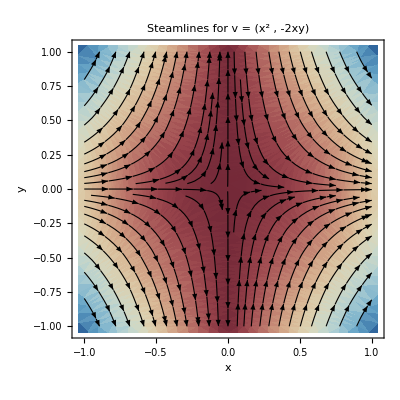

∇·v⃗ = 0

The flow is Incompressible

∇× v⃗ = {0,0,-2 y}

The flow has Vorticity

```mathematica
Remove["Global`*"]
v={x^2,-2x y};
StreamDensityPlot[v,{x,-1,1},{y,-1,1},ColorFunction->"RedBlueTones",StreamStyle->{Black,Thickness[.002]},PlotLabel->Style["Steamlines for v = (x^2 , -2xy)",15,"Graphics"],FrameLabel->{"x","y"} ]
Print["∇·v⃗ = ",Div[Flatten[{v,0}],{x,y,z}]]
Print["The flow is ",Evaluate[If[TrueQ[Div[Flatten[{v,0}],{x,y,z}]==0],Style["Incompressible",Bold],Style["Compressible",Bold]]]]
Print["∇× v⃗ = ",Curl[Flatten[{v,0}],{x,y,z}]]
Print["The flow has ",Evaluate[If[TrueQ[Curl[Flatten[{v,0}],{x,y,z}]=={0,0,0}],Style["No Vorticity",Bold],Style["Vorticity",Bold]]]]
```

{-y,x}

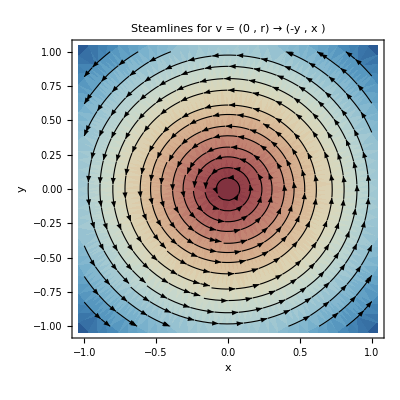

∇·v⃗ = 0

The flow is Incompressible

∇× v⃗ = {0,0,2}

The flow has Vorticity

```mathematica
Remove["Global`*"]
v={0,r};
Curl[Flatten[{v,0}],{r,θ,z},"Cylindrical"];
v=TransformedField["Polar"->"Cartesian",v,{r,θ}->{x,y}]
StreamDensityPlot[v,{x,-1,1},{y,-1,1},ColorFunction->"RedBlueTones",StreamStyle->{Black,Thickness[.002]},PlotLabel->Style["Steamlines for v = (0 , r) → (-y , x )",15,"Graphics"],FrameLabel->{"x","y"} ]
Print["∇·v⃗ = ",Div[Flatten[{v,0}],{x,y,z}]]
Print["The flow is ",Evaluate[If[TrueQ[Div[Flatten[{v,0}],{x,y,z}]==0],Style["Incompressible",Bold],Style["Compressible",Bold]]]]
Print["∇× v⃗ = ",Curl[Flatten[{v,0}],{x,y,z}]]
Print["The flow has ",Evaluate[If[TrueQ[Curl[Flatten[{v,0}],{x,y,z}]=={0,0,0}],Style["No Vorticity",Bold],Style["Vorticity",Bold]]]]
```

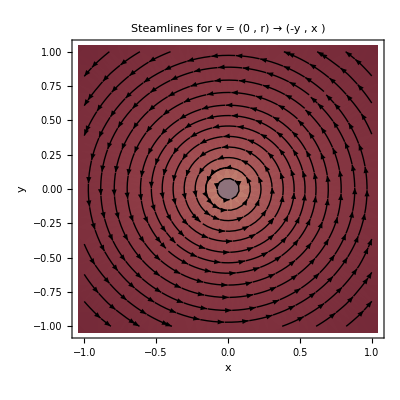

∇·v⃗ = 0

The flow is Incompressible

∇× v⃗ = {0,0,-(2 x^2)/((x^2+y^2)^2)-(2 y^2)/((x^2+y^2)^2)+2/(x^2+y^2)}

The flow has No Vorticity except at r=0, where w=∞

```mathematica
Remove["Global`*"]
v={0,r^-1};
v=TransformedField["Polar"->"Cartesian",v,{r,θ}->{x,y}];
StreamDensityPlot[{v,Log[Norm[v]]},{x,-1,1},{y,-1,1},ColorFunction->"RedBlueTones",StreamStyle->{Black,Thickness[.002]},PlotLabel->Style["Steamlines for v = (0 , r) → (-y , x )",15,"Graphics"],FrameLabel->{"x","y"} ]
Print["∇·v⃗ = ",Div[Flatten[{v,0}],{x,y,z}]]
Print["The flow is ",Evaluate[If[TrueQ[Div[Flatten[{v,0}],{x,y,z}]==0],Style["Incompressible",Bold],Style["Compressible",Bold]]]]
Print["∇× v⃗ = ",Curl[Flatten[{v,0}],{x,y,z}]]
Print["The flow has ",Evaluate[If[TrueQ[Simplify[Curl[Flatten[{v,0}],{x,y,z}]]=={0,0,0}],Style["No Vorticity",Bold],Style["Vorticity",Bold]]]," except at r=0, where w=∞"]
```

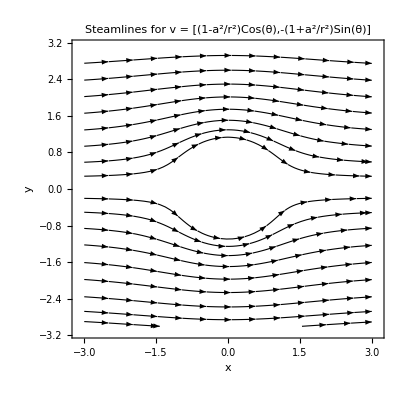

∇·v⃗ = 0

The flow is Incompressible

∇× v⃗ = {0,0,0}

The flow has No Vorticity

```mathematica
Remove["Global`*"]
a=1;
v={(1-a^2/r^2)Cos[θ],-(1+a^2/r^2)Sin[θ]};
v=TransformedField["Polar"->"Cartesian",v,{r,θ}->{x,y}];


StreamPlot[Piecewise[{{v, √(x^2+y^2)≥a}, {0, √(x^2+y^2)< a}}],{x,-3,3},{y,-3,3},ColorFunction->"RedBlueTones",StreamStyle->{Black,Thickness[.002]},PlotLabel->Style["Steamlines for v = [(1-a^2/r^2)Cos(θ),-(1+a^2/r^2)Sin(θ)]",15,"Graphics"],FrameLabel->{"x","y"}]
Print["∇·v⃗ = ",Div[Flatten[{v,0}],{x,y,z}]//PowerExpand//Simplify]
Print["The flow is ",Evaluate[If[TrueQ[Simplify[Div[Flatten[{v,0}],{x,y,z}]==0]],Style["Incompressible",Bold],Style["Compressible",Bold]]]]
Print["∇× v⃗ = ",Simplify[Curl[Flatten[{v,0}],{x,y,z}]]]
Print["The flow has ",Evaluate[If[TrueQ[Simplify[Curl[Flatten[{v,0}],{x,y,z}]]=={0,0,0}],Style["No Vorticity",Bold],Style["Vorticity",Bold]]]]
```

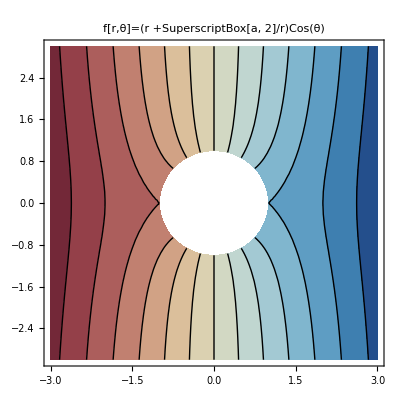

```mathematica
f[x_,y_]=(√(x^2+y^2)+a^2/(√(x^2+y^2)))x/(√(x^2+y^2));
ContourPlot[f[x,y],{x,-3,3},{y,-3,3},RegionFunction->Function[{x,y},√(x^2+y^2)>a],Contours->Range[-3,3,.5],ContourStyle->Black,ColorFunction->"RedBlueTones",PlotLabel->Style["f[r,θ]=(r +SuperscriptBox[a, 2]/r)Cos(θ)",15,"Graphics"]]
```

```mathematica
((1-a^2/r^2)Cos[θ])^2+(-(1+a^2/r^2)Sin[θ])^2/.r->a//PowerExpand//Apart//Expand//Simplify//FullSimplify
```

4 Sin[θ]^2

```mathematica
DSolve[{D[F[x],x,x]+a/(3 b ν)D[F[x] D[F[x],x],x]==0,F''[0]==0,F[0]==0},F,x]
```

{{F→Function[{x},(3 (-b ν+√(b^2 ν^2)))/a]},{F→Function[{x},-(3 (b ν+√(b^2 ν^2)))/a]}}